```mathematica
Bifurcation Analysis
```

Author: Kayla R. S. Hale	Last Revised: Dec. 15, 2021

Cite this work as: 
Hale, K.R.S., Maes, D.P., & Valdovinos, F.S. (2021). Simple mechanisms of plant reproductive benefits yield different dynamics in pollination and seed dispersal mutualisms (in review).

-Bifurcation analysis on , the attack rate by the animal population () on the plant population’s () rewards, interpreted as “foraging efficiency” in the main text
-Using main-text models and notation following Hale et al. 2021
-Solutions were assessed for stability using phase plane analyses (see the other code notebooks)
-Solution curves were colored manually in Adobe Illustrator, green or black for plant or animal equilibrium density (top or bottom panels), respectively
-Solutions for one species that are infeasible for the other were excluded (that is, only solutions where both species’ density are non-negative were included)
-Plants are obligate when   or facultative otherwise; animals are obligate when  or facultative otherwise
NOTE: make sure the variable workspace is clear before plotting (e.g., by quitting the kernal), or solution will appear as horizontal lines (apparently independent of )

## Pollination Mutualism Model

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

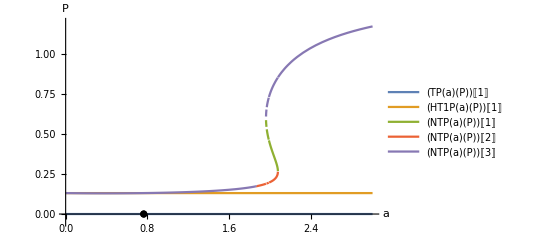

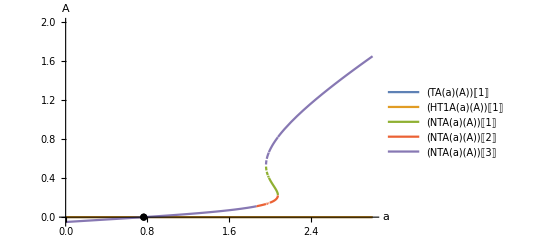

```mathematica
(* Pollination *) 
(* parameters *) 
bP=1.5; f = 0.5; φ=0.5; g=1;sP=0.61; dP=0.67; 
h=0.01;
bA=1; ε=1; sA=2; dA=1.1;

(* intrinsic growth rates for both species (in the absence of mutualism) *) 
rP = bP*f*g-dP; rPmax = rP+bP*φ*g;
rA = bA-dA;

(* condition for transition in dynamics 
-does not strictly hold for infeasible solutions
-derived by inspecting the intercepts of the non-trivial nullclines 
-see Results of Main Text *)
condition = (-rA*sP)/(rP* (ε+h*rA));

(* non-trivial [coexistence] equilibrium *) 
(* both species' densities are > 0 *)
equilibriaNT = Solve[{bP*(f+φ*(a*P)/(1+a*h*P+a*P*A)*A)*g-sP*P-dP==0, bA+ε*(a*P)/(1+a*h*P)-sA*A - dA==0},{P,A}];

(* trivial equilibrium *) 
(* both species' densities are 0 *)
equilibriaT=Solve[{P==0, A==0},{P,A}];

(* half-trivial equilibria *)
(* one species' density is 0 *)
equilibriaHT1=Solve[{bP*(f+φ*(a*P)/(1+a*h*P+a*P*A)*A)*g-sP*P-dP==0, A==0},{P,A}]; (* extinct animals *)
equilibriaHT2=Solve[{P==0,bA+ε*(a*P)/(1+a*h*P)-sA*A - dA==0},{P,A}]; (* extinct plants *)

(* expressions for equilibria as a function of  and species densities () *)
(* notice that since they will be plotted as a function of a, the function outputs are either plant or animal density at equilibrium (e.g., non-trivial equilibrium density NTP or NTA, respectively) *)

(* non-trivial *) 
NTP[a_][P_] := Evaluate[P /. equilibriaNT]
NTA[a_][A_] := Evaluate[A /. equilibriaNT]

(* trivial *)
TP[a_][P_] := Evaluate[P /. equilibriaT]
TA[a_][A_] := Evaluate[A /. equilibriaT]

(* half-trivial *)
HT1P[a_][P_] := Evaluate[P /. equilibriaHT1]
HT1A[a_][A_] := Evaluate[A /. equilibriaHT1]
HT2P[a_][P_] := Evaluate[P /. equilibriaHT2]
HT2A[a_][A_] := Evaluate[A /. equilibriaHT2]

(* plotting the bifurcation diagrams, using different colors for the different equilibria, so it's easy to see transitions in dynamics *) 
(* not automatically calculating if they are stable or not--too computationally intensive *)

(* plant equilibrium density *)
(* layer all the plots on top of each other for one bifurcation diagram, label the condition with a point *)
Show[Plot[{TP[a][P][[1]],HT1P[a][P][[1]],NTP[a][P][[1]],NTP[a][P][[2]],NTP[a][P][[3]]},{a,0,3},PlotLegends->"Expressions",PlotRange->{-0.05,1.2}],ListPlot[{{condition,0}},PlotStyle->Black],AxesLabel->{a,P}]

(* animal equilibrium density *)
Show[Plot[{TA[a][A][[1]],HT1A[a][A][[1]],NTA[a][A][[1]],NTA[a][A][[2]],NTA[a][A][[3]]},{a,0,3},PlotLegends->"Expressions",PlotRange->{-0.05,2}],ListPlot[{{condition,0}},PlotStyle->Black],AxesLabel->{a,A}]
```

## Seed Dispersal Mutualism: Germination Model

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

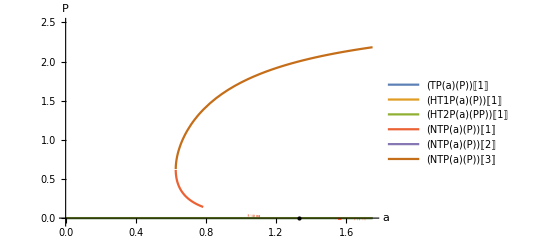

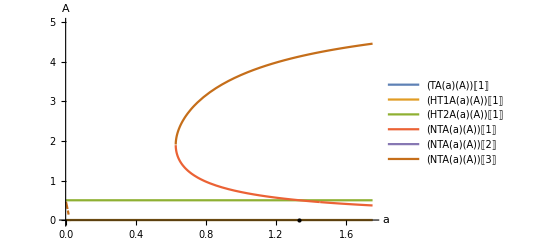

```mathematica
(* Germination *) 
(* parameters *) 
bP=1; f = 1; g=0.5;γ =0.5;sP=0.05; dP=0.7; 
h=1;
bA=1; ε=1; sA=0.2; dA=0.9;

(* intrinsic growth rates for both species (in the absence of mutualism) *) 
rP = bP*f*g-dP; rPmax = rP+bP*f*γ;
rA = bA-dA;

(* conditions for transition in dynamics 
-do not strictly hold for infeasible solutions
-derived by inspecting the intercepts of the non-trivial nullclines 
-see Results in Main Text *)
condition1 = (-rA*sP)/(rP* (ε+h*rA));
condition2 = (-rP*sA)/(rPmax * rA);

(* non-trivial equilibrium *) 
equilibriaNT = Solve[{bP*f*(g+γ*(a*A)/(1+a*h*P+a*A))-sP*P-dP==0,bA+ε*(a*P)/(1+a*h*P)-sA*A - dA==0},{P,A}];

(* trivial equilibrium *) 
equilibriaT=Solve[{P==0, A==0},{P,A}];

(* half-trivial equilibria *)
equilibriaHT1=Solve[{bP*f*(g+γ*(a*A)/(1+a*h*P+a*A))-sP*P-dP==0, A==0},{P,A}]; (* extinct animals *)
equilibriaHT2=Solve[{P==0, bA+ε*(a*P)/(1+a*h*P)-sA*A - dA==0},{P,A}]; (* extinct plants *) 

(* expressions for equilibria as a function of  and species densities () *)

(* non-trivial *)
NTP[a_][P_] := Evaluate[P /. equilibriaNT]
NTA[a_][A_] := Evaluate[A /. equilibriaNT]

(* trivial *) 
TP[a_][P_] := Evaluate[P /. equilibriaT]
TA[a_][A_] := Evaluate[A /. equilibriaT]

(* half-trivial *)
HT1P[a_][P_] := Evaluate[P /. equilibriaHT1]
HT1A[a_][A_] := Evaluate[A /. equilibriaHT1]
HT2P[a_][P_] := Evaluate[P /. equilibriaHT2]
HT2A[a_][A_] := Evaluate[A /. equilibriaHT2]

(* plotting the bifurcation diagrams, using different colors for the different equilibria, so it's easy to see transitions in dynamics *) 
(* not automatically calculating if they are stable or not--too computationally intensive *)

(* plant equilibrium density *)
(* layer all the plots on top of each other for one bifurcation diagram, label the condition with a point *)
Show[Plot[{TP[a][P][[1]],HT1P[a][P][[1]],HT2P[a][PP][[1]],NTP[a][P][[1]],NTP[a][P][[2]],NTP[a][P][[3]]},{a,0,1.75},PlotLegends->"Expressions",PlotRange->{-0.05,2.5}],Graphics[Point[{condition2,0}]],AxesLabel->{a,P}]

(* animal equilibrium density *)
Show[Plot[{TA[a][A][[1]],HT1A[a][A][[1]],HT2A[a][A][[1]],NTA[a][A][[1]],NTA[a][A][[2]],NTA[a][A][[3]]},{a,0,1.75},PlotLegends->"Expressions",PlotRange->{-0.05,5}],Graphics[Point[{condition2,0}]],AxesLabel->{a,A}]
```

## Seed Dispersal Mutualism: Negative-Density Dependence Model

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

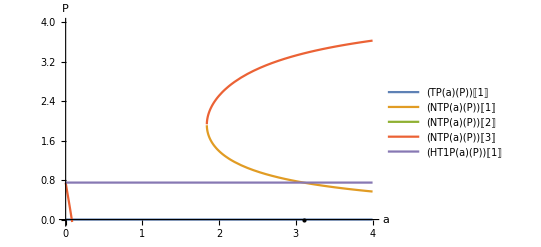

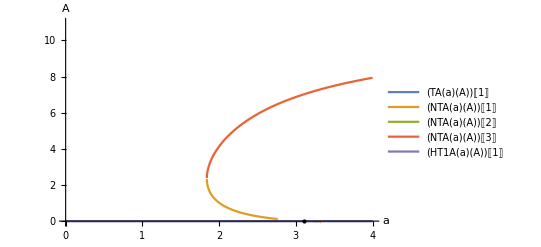

```mathematica
(* Negative Denisty-Dependence *) 
(* parameters *) 
bP=1; f = 1; g=1;sP=0.2; σ =0.2;dP=0.85; 
h=0.5;
bA=1; ε=0.93; sA=0.08; dA=2;

(* intrinsic growth rates for both species (in the absence of mutualism) *) 
rP = bP*f*g-dP;
rA = bA-dA;

(* condition for transition in dynamics 
-does not strictly hold for infeasible solutions
-derived by inspecting the intercepts of the non-trivial nullclines 
-see Results in Main Text *)
condition1 = (-rA*sP)/(rP* (ε+h*rA));

(* non-trivial equilibrium *) 
equilibriaNT = Solve[{bP*f*g-(sP-σ*(a*A)/(1+a*h*P+a*A))*P-dP==0 ,bA+ε*(a*P)/(1+a*h*P)-sA*A - dA==0},{P,A}];

(* trivial equilibrium *) 
equilibriaT=Solve[{P==0, A==0},{P,A}];

(* half-trivial equilibria *)
equilibriaHT1=Solve[{bP*f*g-(sP-σ*(a*A)/(1+a*h*P+a*A))*P-dP==0 , A==0},{P,A}]; (* extinct animals *) 
equilibriaHT2=Solve[{P==0,bA+ε*(a*P)/(1+a*h*P)-sA*A - dA==0},{P,A}]; (* extinct plants *)

(* expressions for equilibria as a function of  and species densities () *)

(* non-trivial *)
NTP[a_][P_] := Evaluate[P /. equilibriaNT]
NTA[a_][A_] := Evaluate[A /. equilibriaNT]

(* trivial *) 
TP[a_][P_] := Evaluate[P /. equilibriaT]
TA[a_][A_] := Evaluate[A /. equilibriaT]

(* half-trivial *)
HT1P[a_][P_] := Evaluate[P /. equilibriaHT1]
HT1A[a_][A_] := Evaluate[A /. equilibriaHT1]
HT2P[a_][P_] := Evaluate[P /. equilibriaHT2]
HT2A[a_][A_] := Evaluate[A /. equilibriaHT2]

(* plant equilibrium density *)
(* layer all the plots on top of each other for one bifurcation diagram, label the condition with a point *)
Show[Plot[{TP[a][P][[1]],NTP[a][P][[1]],NTP[a][P][[2]],NTP[a][P][[3]],HT1P[a][P][[1]]},{a,0,4},PlotLegends->"Expressions",PlotRange->{-0.05,4}],Graphics[Point[{condition1,0}]],AxesLabel->{a,P}]

(* animal equilibrium density *)
Show[Plot[{TA[a][A][[1]],NTA[a][A][[1]],NTA[a][A][[2]],NTA[a][A][[3]],HT1A[a][A][[1]]},{a,0,4},PlotLegends->"Expressions",PlotRange->{-0.05,11}],Graphics[Point[{condition1,0}]],AxesLabel->{a,A}]
```